```mathematica
SetDirectory[NotebookDirectory[]];
Get["betas.m"];
```

```mathematica
kruzhok[text_,{x_,y_},fontsize_,r_]:={Circle[{x,y},r],{White,Disk[{x,y},0.95r]},Text[Style[text,fontsize,"Times"],{x,y}]};
```

## |1|1|1|:

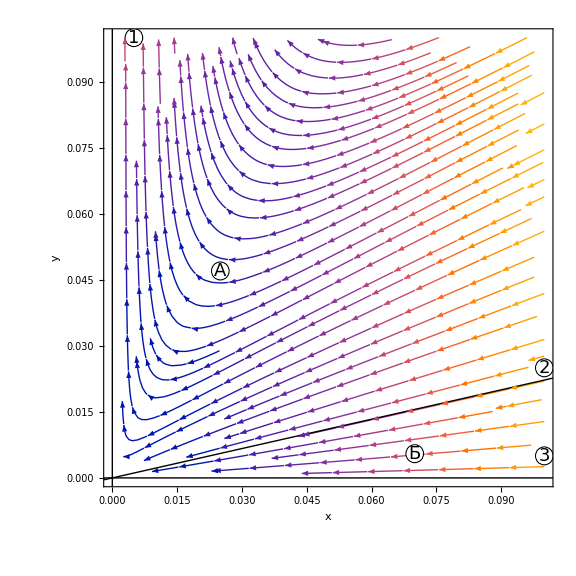

figures/00111xy.pdf

```mathematica
StreamPlot[{-7 x^2,-8 x y+(9 y^2)/2},{x,0,0.1},{y,0,0.1},FrameLabel->{"x","y"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{0,0},{1,2/9}],
kruzhok["1",{0.005,0.1},18,0.002],kruzhok["2",{0.1,0.025},18,0.002],kruzhok["3",{0.1,0.005},18,0.002],kruzhok["А",{0.025,0.047},18,0.002],kruzhok["Б",{0.07,0.0055},18,0.002]
},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/00111xy.pdf",%]
```

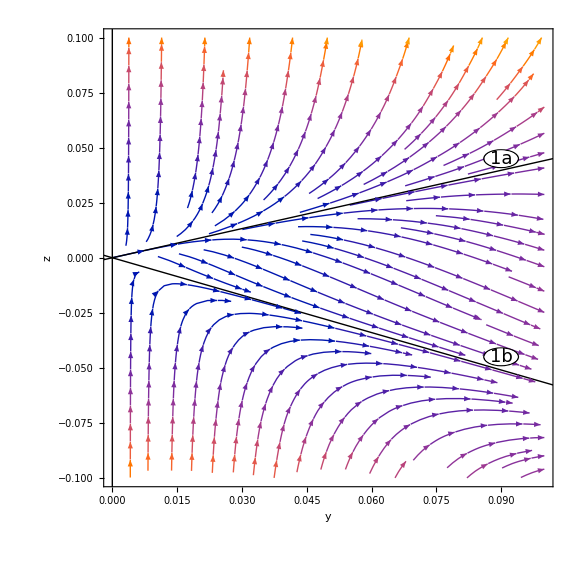

figures/00111in1yz.pdf

```mathematica
StreamPlot[{9/2 y^2,6z(2z+y)-3y^2},{y,0,0.1},{z,-0.1,0.1},FrameLabel->{"y","z"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,(-1-Sqrt[65])/16}],InfiniteLine[{0,0},{1,(-1+Sqrt[65])/16}],
kruzhok["1a",{0.09,0.045},18,0.004],kruzhok["1b",{0.09,-0.045},18,0.004]},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/00111in1yz.pdf",%]
```

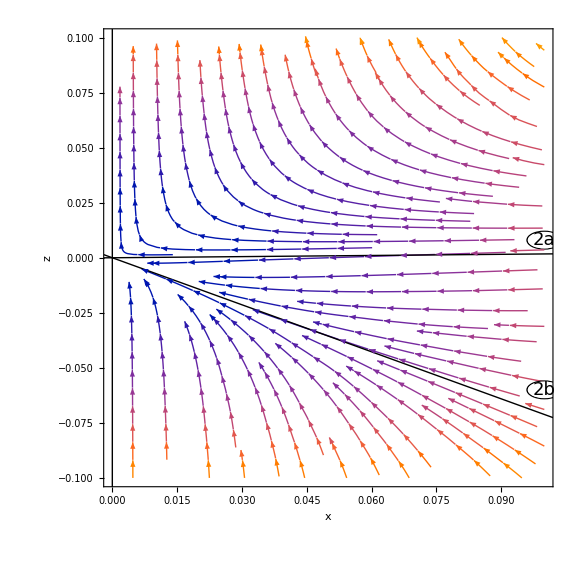

figures/00111in2x3z.pdf

```mathematica
StreamPlot[{-7x^2,6z(2z+2/9 x)-4/9 x^2},{x,0,0.1},{z,-0.1,0.1},FrameLabel->{"x","z"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,(-25-Sqrt[689])/72}],InfiniteLine[{0,0},{1,(-25+Sqrt[689])/72}],
kruzhok["2a",{0.1,0.008},18,0.004],kruzhok["2b",{0.1,-0.06},18,0.004]},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/00111in2x3z.pdf",%]
```

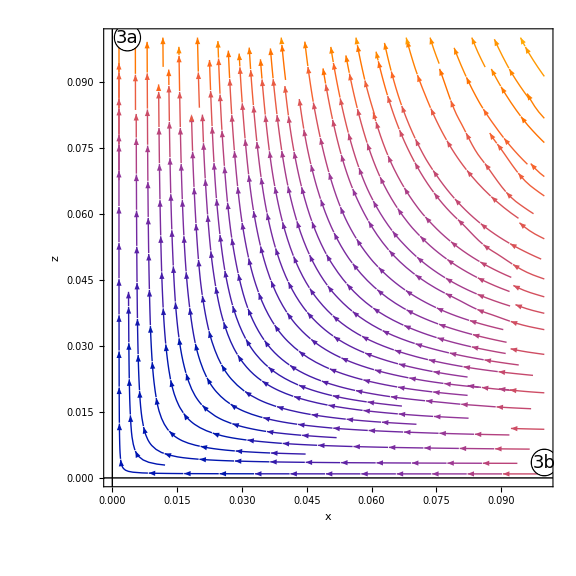

figures/00111in3x3z.pdf

```mathematica
StreamPlot[{-7x^2,12z^2},{x,0,0.1},{z,0,0.1},FrameLabel->{"x","z"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],kruzhok["3a",{0.0035,0.1},18,0.003],kruzhok["3b",{0.1,0.0035},18,0.003]},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/00111in3x3z.pdf",%]
```

```mathematica
{(ydot[1,1,1]x-xdot[1,1,1]y)/x^3,(zdot[1,1,1]x-xdot[1,1,1]z)/x^3}/.{y->Y x, z->Z x}//FullSimplify
```

{1/2 Y (-2+9 Y),-3 Y^2+6 Y Z+Z (7+12 Z)}

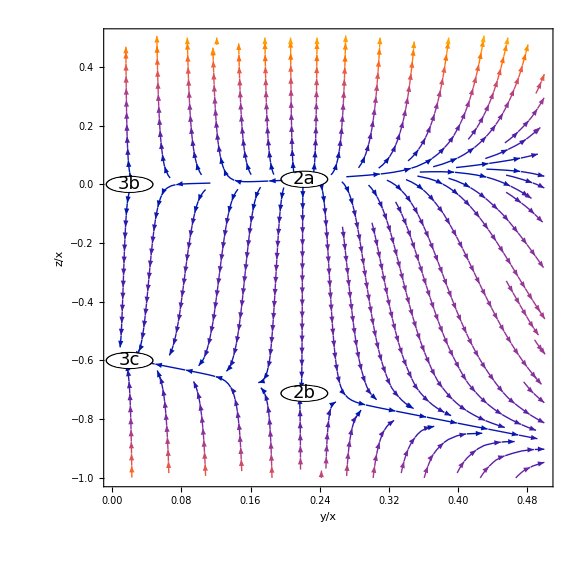

figures/111allseps.pdf

```mathematica
StreamPlot[{1/2 Y (-2+9 Y),-3 Y^2+6 Y Z+Z (7+12 Z)},{Y,0,0.5},{Z,-1,0.5},FrameLabel->{"y/x","z/x"},Epilog->{kruzhok["2a",{2/9,(-25+Sqrt[689])/72},18,0.027],kruzhok["2b",{2/9,(-25-Sqrt[689])/72},18,0.027],kruzhok["3b",{0.02,0},18,0.027],kruzhok["3c",{0.02,-0.6},18,0.027]},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True,StreamPoints->Fine]
Export["figures/111allseps.pdf",%]
```

## 2,1,0:

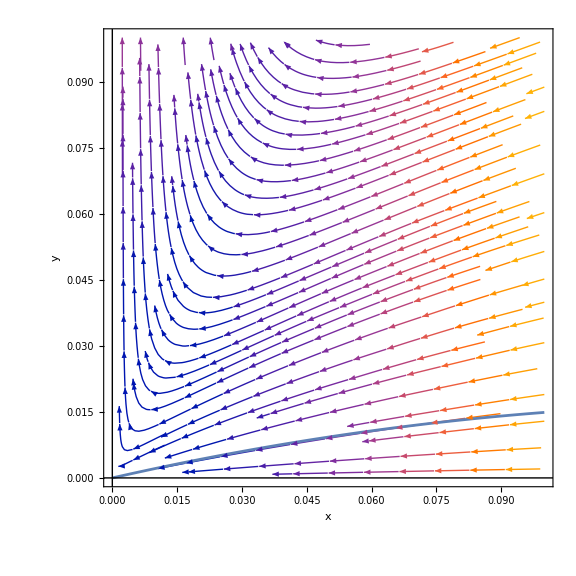

figures/00210x3y.pdf

```mathematica
Show[
StreamPlot[
{-7 x^2-26 x^3-2 x^2 y,-8 x y+(9 y^2)/2},{x,0,0.1},{y,0,0.1},
FrameLabel->{"x","y"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}]}
,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True],
ParametricPlot[{x,2/9 x-119/162 x^2},{x,0,0.1}]
]
Export["figures/00210x3y.pdf",%]
```

## 1,1,1;1;1

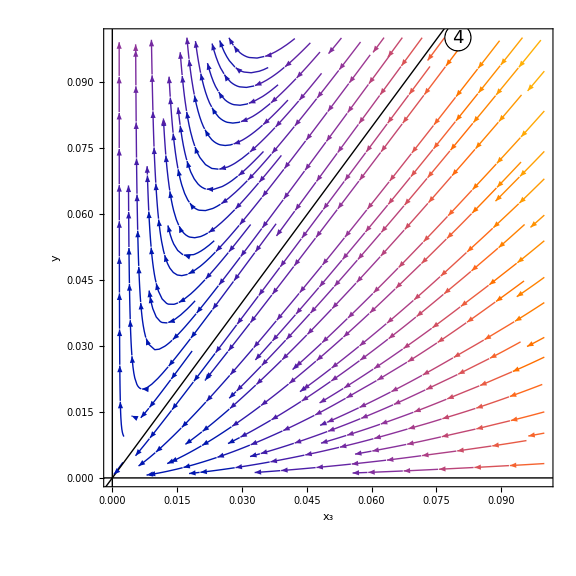

figures/11111x2breveis0.pdf

```mathematica
StreamPlot[{-7 x3^2,y (-(493 x3)/38+(9 y)/2)},{x3,0,0.1},{y,0,0.1},FrameLabel->{"x_3","y"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{0,0},{171/227,1}],kruzhok["4",{0.08,0.1},18,0.003]} ,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/11111x2breveis0.pdf",%]
```

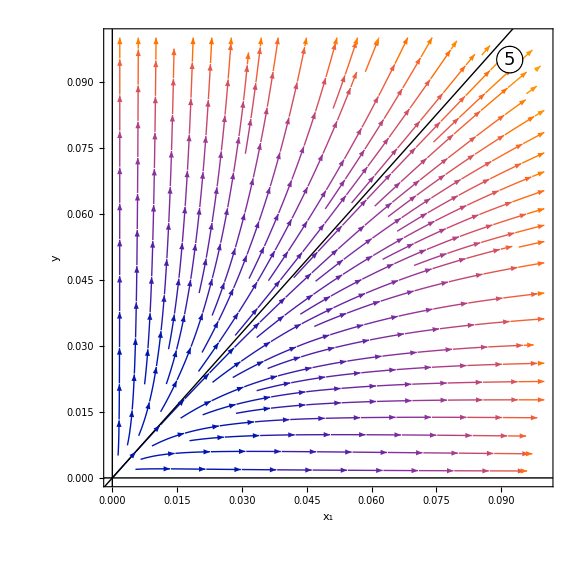

figures/11111nox2x3.pdf

```mathematica
StreamPlot[{(41 x1^2)/10,-(17 x1 y)/20+(9 y^2)/2},{x1,0,0.1},{y,0,0.1},FrameLabel->{"x_1","y"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{0,0},{10/11,1}],kruzhok["5",{0.092,0.095},18,0.003]} ,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/11111nox2x3.pdf",%]
```

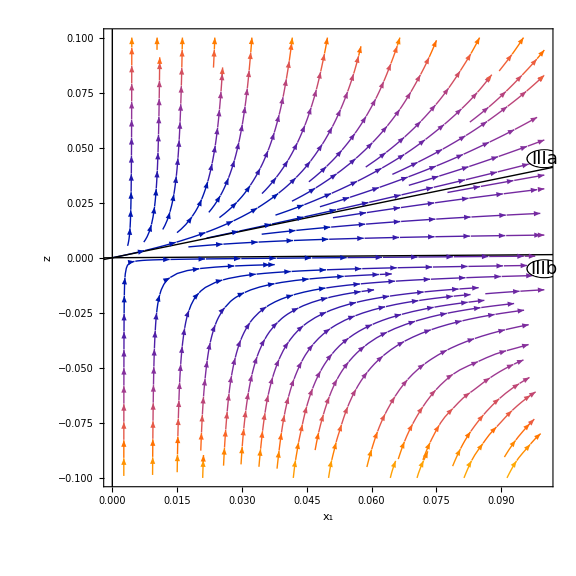

figures/11111inIIIx2is0.pdf

```mathematica
StreamPlot[{(41 x1^2)/10,(27 x1^2)/400-(9 x1 z)/10+12 z^2},{x1,0,0.1},{z,-0.1,0.1},FrameLabel->{"x_1","z"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1/27 (1000-160 √34),1}],InfiniteLine[{0,0},{1/27 (1000+160 √34),1}],kruzhok["IIIa",{0.1,0.045},18,0.004],kruzhok["IIIb",{0.1,-0.005},18,0.004]} ,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/11111inIIIx2is0.pdf",%]
```

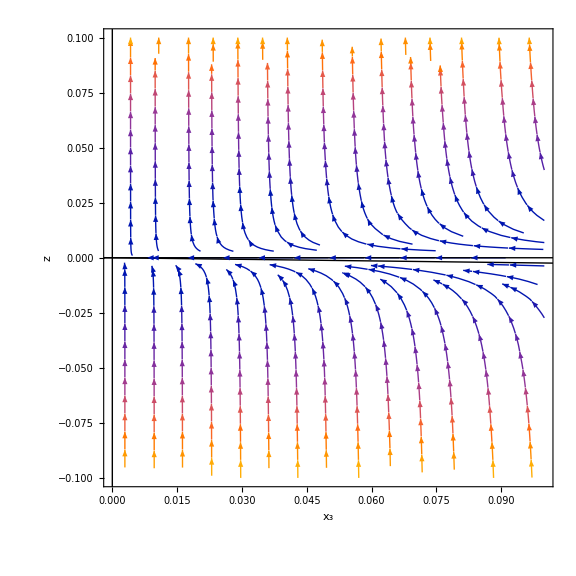

```mathematica
StreamPlot[{-7 x3^2,164/27 (25+4 √34) z^2},{x3,0,0.1},{z,-0.1,0.1},
FrameLabel->{"x_3","z"},
Epilog->{InfiniteLine[{0,0},{-164/189(25+4Sqrt[34]),1}],InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}]},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
```

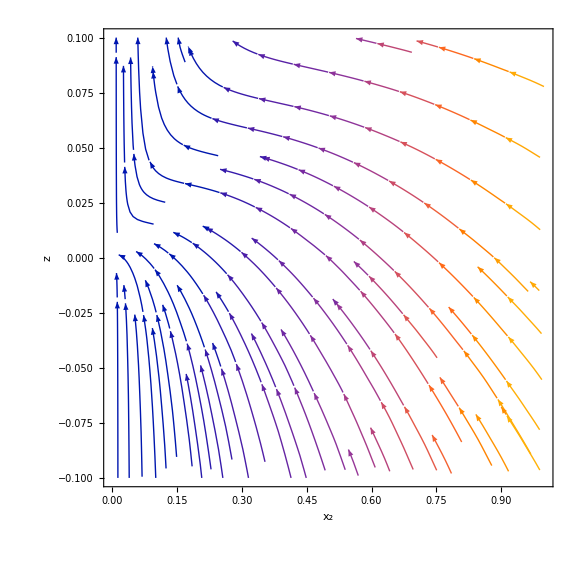

figures/11111inIIIx1is0.pdf

```mathematica
StreamPlot[{-(19 x2^2)/6,(9 x2^2)/16-(9 x2 z)/2+12 z^2},{x2,0,1},{z,-0.1,0.1}, FrameLabel->{"x_2","z"},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True,StreamPoints->Fine]
Export["figures/11111inIIIx1is0.pdf",%]
```

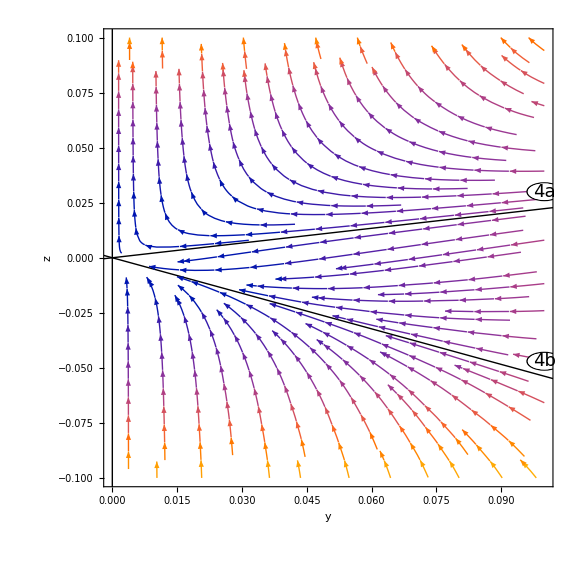

figures/11111in4.pdf

```mathematica
StreamPlot[{-(1197 y^2)/227,-(296859 y^2)/206116-(339 y z)/227+12 z^2},{y,0,0.1},{z,-0.1,0.1},
FrameLabel->{"y","z"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{(908 (143-√119402))/98953,1}],InfiniteLine[{0,0},{(908 (143+√119402))/98953,1}],kruzhok["4a",{0.1,0.03},18,0.004],kruzhok["4b",{0.1,-0.047},18,0.004]} ,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/11111in4.pdf",%]
```

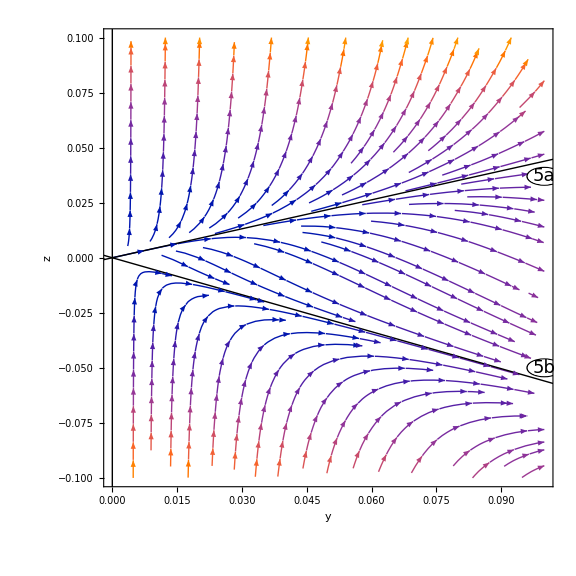

figures/11111in5.pdf

```mathematica
StreamPlot[{(41 y^2)/11,-(1425 y^2)/484+(57 y z)/11+12 z^2},{y,0,0.1},{z,-0.1,0.1},FrameLabel->{"y","z"},
Epilog->{InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{(44 (8-√4339))/1425,1}],InfiniteLine[{0,0},{(44 (8+√4339))/1425,1}],kruzhok["5a",{0.1,0.037},18,0.004],kruzhok["5b",{0.1,-0.05},18,0.004]} ,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/11111in5.pdf",%]
```

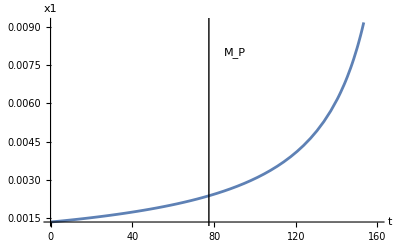
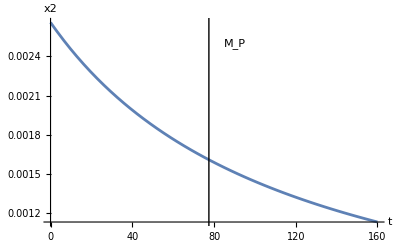
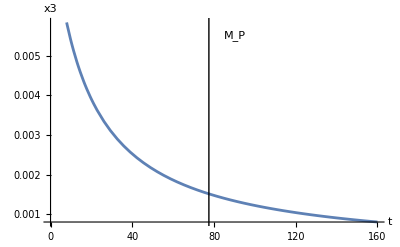
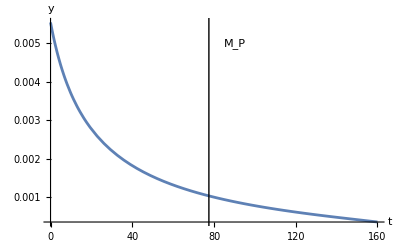
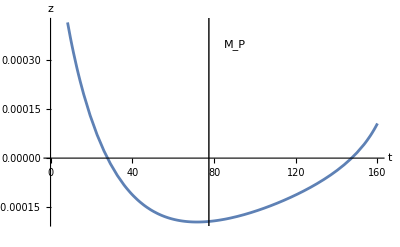

figures/11111exp.pdf

```mathematica
Block[{sol,tm=160},
sol=NDSolve[
{x1'[t]==(x1dot[1,1,1,1,1]/.{x1->x1[t],x2->x2[t],x3->x3[t],y->y[t],z->z[t]}),x2'[t]==(x2dot[1,1,1,1,1]/.{x1->x1[t],x2->x2[t],x3->x3[t],y->y[t],z->z[t]}),x3'[t]==(x3dot[1,1,1,1,1]/.{x1->x1[t],x2->x2[t],x3->x3[t],y->y[t],z->z[t]}),y'[t]==(ydot[1,1,1,1,1]/.{x1->x1[t],x2->x2[t],x3->x3[t],y->y[t],z->z[t]}),z'[t]==(zdot[1,1,1,1,1]/.{x1->x1[t],x2->x2[t],x3->x3[t],y->y[t],z->z[t]}), 
x1[0]==x10,x2[0]==x20,x3[0]==x30,y[0]==y10,z[0]==z0}/.expdata
,{x1[t],x2[t],x3[t],y[t],z[t]},{t,0,tm}][[1]];
{Plot[x1[t]/.sol,{t,0,tm},AxesLabel->{"t","x1"},Epilog->{Text["M_P",{90,0.008}],InfiniteLine[{77.5,0},{0,1}]}],
Plot[x2[t]/.sol,{t,0,tm},AxesLabel->{"t","x2"},Epilog->{Text["M_P",{90,0.0025}],InfiniteLine[{77.5,0},{0,1}]}],
Plot[x3[t]/.sol,{t,0,tm},AxesLabel->{"t","x3"},Epilog->{Text["M_P",{90,0.0055}],InfiniteLine[{77.5,0},{0,1}]}],
Plot[y[t]/.sol,{t,0,tm},AxesLabel->{"t","y"},Epilog->{Text["M_P",{90,0.005}],InfiniteLine[{77.5,0},{0,1}]}],
Plot[z[t]/.sol,{t,0,tm},AxesLabel->{"t","z"},Epilog->{Text["M_P",{90,0.00035}],InfiniteLine[{77.5,0},{0,1}]}]}
]
Export["figures/11111exp.pdf",%]
```

## |1,1,1|1,1|1|

```mathematica
x3dot[111111]=x3dot[1,1,1,1,1,1];
y1dot[111111]=y1dot[1,1,1,1,1,1];
y2dot[111111]=y2dot[1,1,1,1,1,1];
zdot[111111]=zdot[1,1,1,1,1,1];
```

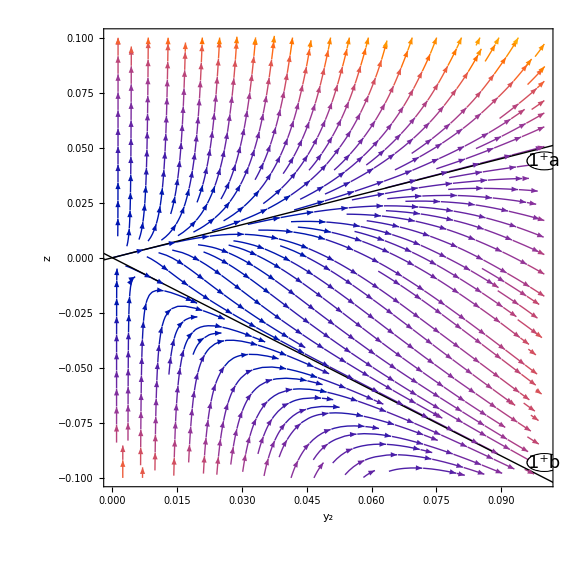

figures/111111in1plusy2z.pdf

```mathematica
StreamPlot[{y2dot[111111],zdot[111111]}/.{y1->y2,x1->0,x2->0,x3->0},{y2,0,0.1},{z,-0.1,0.1},FrameLabel->{"y_2","z"},Epilog->{InfiniteLine[{0,0},{-1,1}],InfiniteLine[{0,0},{2,1}],kruzhok["1^+a",{0.1,0.044},18,0.004],kruzhok["1^+b",{0.1,-0.093},18,0.004]} ,ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True,StreamPoints->Fine]
Export["figures/111111in1plusy2z.pdf",%]
```

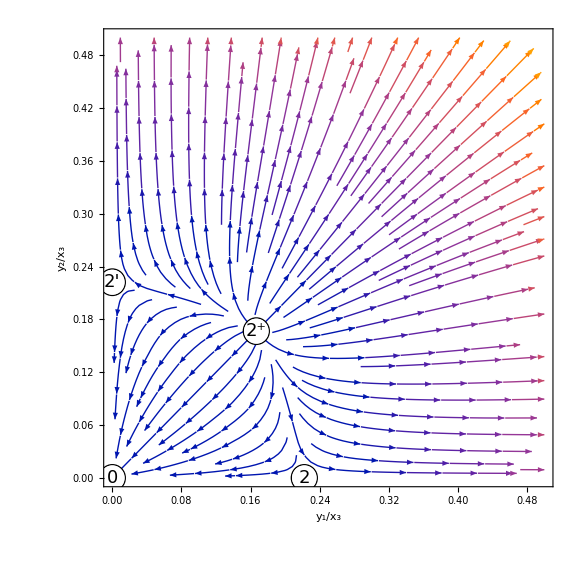

figures/111111alltwos.pdf

```mathematica
StreamPlot[{(y1dot[111111]x3-x3dot[111111]y1)/x3^3,(y2dot[111111]x3-x3dot[111111]y2)/x3^3}/.{x1->0,x2->0,y1->Y1 x3, y2->Y2 x3}//FullSimplify,{Y1,0,0.5},{Y2,0,0.5},FrameLabel->{"y_1/x_3","y_2/x_3"},Epilog->{kruzhok["0",{0,0},18,0.015],kruzhok["2'",{0,2/9},18,0.015],kruzhok["2^+",{1/6,1/6},18,0.015],kruzhok["2",{2/9,0},18,0.015]},ImageSize->Large,LabelStyle->{FontSize->18,FontFamily->"Times"},Frame->True]
Export["figures/111111alltwos.pdf",%]
```